```mathematica
ℏ=QuantityMagnitude[Entity["PhysicalConstant","ReducedPlanckConstant"][EntityProperty["PhysicalConstant","Value"]]];
me=QuantityMagnitude[LinguisticAssistant];

LinInterp[dataset_,row_,col_]:=Module[{func,interpval},
func=LinearModelFit[{{row-1,Normal[dataset[[row-1,col]]]},{row+1,Normal[dataset[[row+1,col]]]}},x,x];
interpval=func[row]
]

KParallel[E_,θ_]:=Module[{kpar,Enew},
Enew=E*1.602×10^-19;
kpar=Sin[Pi/180*θ]*Sqrt[2*me*Enew]/ℏ;
kpar=kpar/(10^(10))
]
```

```mathematica
file=SystemDialogInput["FileOpen"];
filepath=StringReplace[#,StringExtract[#,"/"->-1]->""]&[file];

datafile=SemanticImport[file,ExcludedLines->Range[1,6],HeaderLines->1];

movingavggm1=ArrayPad[MovingAverage[Normal[datafile[[All,"gm1"]]],5],{5-1,0},"Fixed"];
movingavggm2=ArrayPad[MovingAverage[Normal[datafile[[All,"gm2"]]],5],{5-1,0},"Fixed"];
subtractedmeangm1=(Subtract@@@Transpose[{Normal[datafile[[All,"gm1"]]],movingavggm1}]);
subtractedmeangm2=(Subtract@@@Transpose[{Normal[datafile[[All,"gm2"]]],movingavggm2}]);

gm1droppos=Flatten[Position[subtractedmeangm1,x_/;x>StandardDeviation[subtractedmeangm1]*5]];
gm2droppos=Flatten[Position[subtractedmeangm2,x_/;x>StandardDeviation[subtractedmeangm2]*5]];


datafile=ReplacePart[datafile,{#,"gm1"}->LinInterp[datafile,#,"gm1"]&/@gm1droppos];
datafile=ReplacePart[datafile,{#,"gm2"}->LinInterp[datafile,#,"gm2"]&/@gm2droppos];

datafile=datafile[GroupBy["theta"]];


gm1counts={};
gm2counts={};
samplecurrent={};
thetas={};
energy={};

For[i=1,i<=Dimensions[datafile][[1]],i++,
For[j=1,j<=Dimensions[GroupBy[datafile[[1]],"en"]][[1]],j++,
AppendTo[gm1counts,Total[GroupBy[datafile[[i]],"en"][[j]][[All,"gm1"]]]];
AppendTo[gm2counts,Total[GroupBy[datafile[[i]],"en"][[j]][[All,"gm2"]]]];
AppendTo[thetas,Round[GroupBy[datafile[[i]],"en"][[j]][[1,"theta"]],0.1]];
AppendTo[energy,GroupBy[datafile[[i]],"en"][[j]][[1,"en"]]];
AppendTo[samplecurrent,Mean[-10^6*Normal[GroupBy[datafile[[i]],"en"][[j]][[All,"6487c"]]]]];
]
]

finaldata=GroupBy[Dataset@MapThread[<|"theta"->#1,"en"->#2,"gm1"->#3,"gm2"->#4,"current"->#5|> &, {thetas,energy,gm1counts,gm2counts,samplecurrent}],"theta"];
datarange=Range[1,Dimensions[finaldata][[1]]];
```

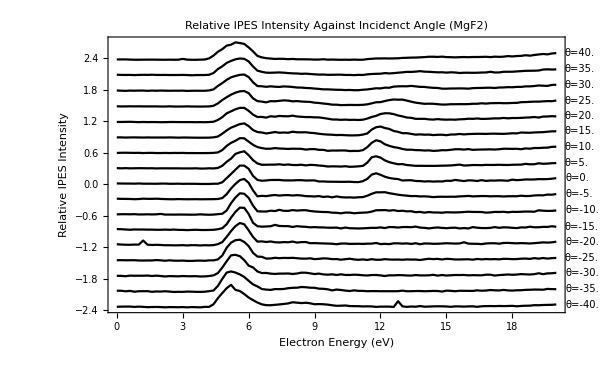

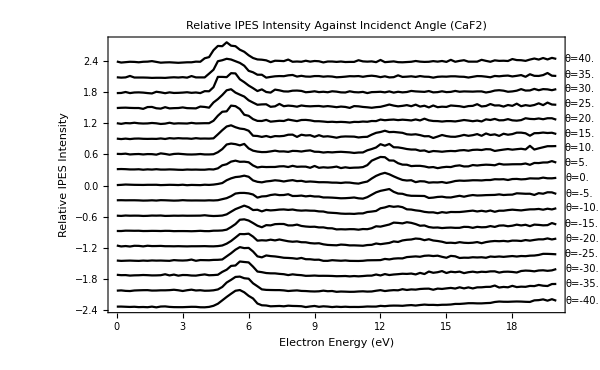

```mathematica
ListLinePlot[Labeled[Transpose[{Normal[finaldata[[#]][[All,"en"]]],Normalize[Normal[finaldata[[#]][[All,"gm1"]]]]+finaldata[[#]][[1,"theta"]]/Length[datarange]}],
"θ="<>ToString[finaldata[[#]][[1,"theta"]]],
LabelStyle->{Black,10,FontFamily->"Times"}]&/@datarange,PlotRange->All,
PlotStyle->Black,
ImageSize->600,
Frame->True,
FrameLabel->{"Electron Energy (eV)","Relative IPES Intensity"},
LabelStyle->{Black,14,FontFamily->"Times"},
Axes->False,
FrameStyle->Directive[Black,12,FontFamily->"Times"],PlotLabel->Style["Relative IPES Intensity Against Incidenct Angle (MgF2)",Black,14,FontFamily->"Times"]
]

ListLinePlot[Labeled[Transpose[{Normal[finaldata[[#]][[All,"en"]]],Normalize[Normal[finaldata[[#]][[All,"gm2"]]]]+finaldata[[#]][[1,"theta"]]/Length[datarange]}],
"θ="<>ToString[finaldata[[#]][[1,"theta"]]],
LabelStyle->{Black,10,FontFamily->"Times"}]&/@datarange,PlotRange->All,
PlotStyle->Black,
ImageSize->600,
Frame->True,
FrameLabel->{"Electron Energy (eV)","Relative IPES Intensity"},
LabelStyle->{Black,14,FontFamily->"Times"},
Axes->False,
FrameStyle->Directive[Black,12,FontFamily->"Times"],PlotLabel->Style["Relative IPES Intensity Against Incidenct Angle (CaF2)",Black,14,FontFamily->"Times"]]
```

```mathematica
kpar=KParallel[energy[[#]],thetas[[#]]]&/@Range[Length[thetas]];

ListContourPlot[Transpose[{kpar,energy,gm1counts}],ColorFunction->GrayLevel,Contours->50,ContourStyle->None,
PlotLabel->Style["E-k Map for MgF2",Black,14,FontFamily->"Times"],
Axes->False,
Frame->True,
FrameLabel->{"k|| (Å)","Electron Energy (eV)"},
LabelStyle->{Black,14,FontFamily->"Times"},
FrameStyle->Directive[Black,14,FontFamily->"times"],
ImageSize->400,
PlotLegends->Placed[BarLegend[Automatic,LabelStyle->Directive[{14,FontFamily->"Times", FontColor->Black}],LegendLabel->Placed[Style["GM Tube Detections (counts/μA s)", 14,FontFamily->"Times", FontColor->Black],Right,Rotate[#,90 Degree]&]],Right]
]

ListContourPlot[Transpose[{kpar,energy,gm2counts}],ColorFunction->GrayLevel,Contours->50,ContourStyle->None,
PlotLabel->Style["E-k Map for CaF2",Black,14,FontFamily->"Times"],
Axes->False,
Frame->True,
FrameLabel->{"k|| (Å)","Electron Energy (eV)"},
LabelStyle->{Black,14,FontFamily->"Times"},
FrameStyle->Directive[Black,14,FontFamily->"times"],
ImageSize->400,
PlotLegends->Placed[BarLegend[Automatic,LabelStyle->Directive[{14,FontFamily->"Times", FontColor->Black}],LegendLabel->Placed[Style["GM Tube Detections (counts/μA s)", 14,FontFamily->"Times", FontColor->Black],Right,Rotate[#,90 Degree]&]],Right]
]
```

-Graphics-

-Graphics-

```mathematica
Manipulate[
testk=KParallel[energy[[#]]-Δ,thetas[[#]]]&/@Range[Length[thetas]];
Grid[{{ListContourPlot[Transpose[{testk,energy-Δ,gm1counts}],ColorFunction->GrayLevel,Contours->50,ContourStyle->None],
ListContourPlot[Transpose[{testk,energy-Δ,gm2counts}],ColorFunction->GrayLevel,Contours->50,ContourStyle->None]}}],
{Δ,0,6}
]
```